(* Jose Dario Sanchez *)
(* josedario@ucla.edu *)
(* ID: 004-505-398 *)
(* Homework #3 *)

The following plot displays the original Square-Wave Pulse Train:

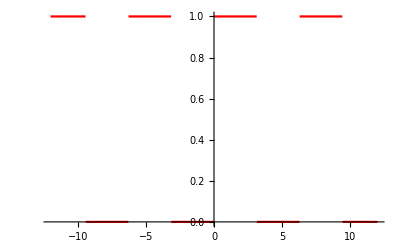

```mathematica
ClearAll["Global`*"]

pulseTrain=SquareWave[{0,1},x/(2*Pi)];

Print["The following plot displays the original Square-Wave Pulse Train:"]
Plot[pulseTrain,{x,-12,12},PlotStyle->Red]
```

The following plot compares the a_n and b_n Series Expansions to the 20th term:

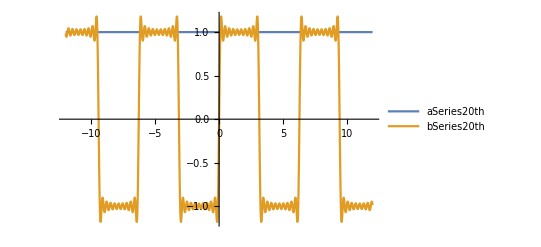

```mathematica
ClearAll["Global`*"]

pulseTrain=SquareWave[{0,1},x/(2*Pi)];
aSeries20th=FourierCosSeries[pulseTrain,x,20];
bSeries20th=FourierSinSeries[pulseTrain,x,20];

Print["The following plot compares the a_n and b_n Series Expansions to the 20th term:"]
Plot[{aSeries20th,bSeries20th},{x,-12,12},PlotLegends->"Expressions"]
```

The following plot compares the original Pulse Train to its Fourier Series expansion to the 20th term:

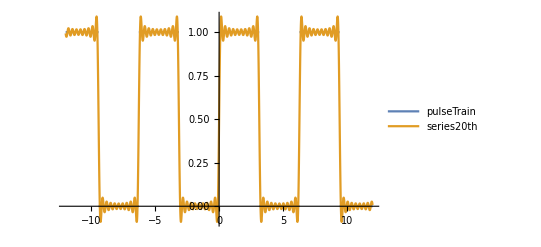

```mathematica
ClearAll["Global`*"]

pulseTrain=SquareWave[{0,1},x/(2*Pi)];
series20th=FourierSeries[pulseTrain,x,20];

Print["The following plot compares the original Pulse Train to its Fourier Series expansion to the 20th term:"]
Plot[{pulseTrain,series20th},{x,-12,12},PlotLegends->"Expressions"]
```

The following plot compares the original Pulse Train to its Fourier Series expansion to the 30th term:

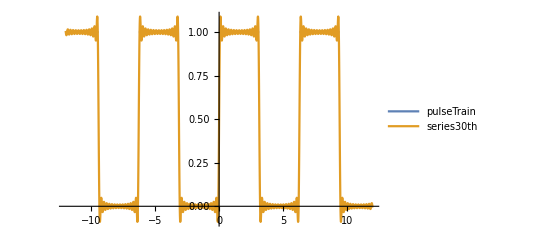

```mathematica
ClearAll["Global`*"]

pulseTrain=SquareWave[{0,1},x/(2*Pi)];
series30th=FourierSeries[pulseTrain,x,30];

Print["The following plot compares the original Pulse Train to its Fourier Series expansion to the 30th term:"]
Plot[{pulseTrain,series30th},{x,-12,12},PlotLegends->"Expressions"]
```

The following plot compares the original Pulse Train to its Fourier Series expansion to the 100th term:

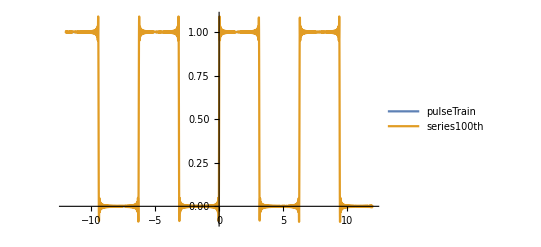

```mathematica
ClearAll["Global`*"]

pulseTrain=SquareWave[{0,1},x/(2*Pi)];
series100th=FourierSeries[pulseTrain,x,100];

Print["The following plot compares the original Pulse Train to its Fourier Series expansion to the 100th term:"]
Plot[{pulseTrain,series100th},{x,-12,12},PlotLegends->"Expressions"]
```

The following graph displays the function representing the positive portions of a sine wave:

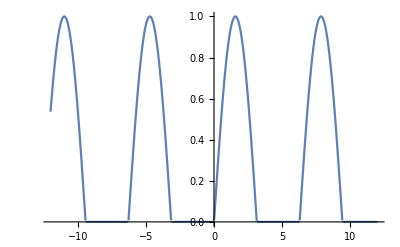

```mathematica
ClearAll["Global`*"]

sinHalfWave=Piecewise[{{Sin[ωt],Sin[ωt]>0},{0,Sin[ωt]<0}}];

Print["The following graph displays the function representing the positive portions of a sine wave:"]
Plot[sinHalfWave,{ωt,-12,12}]
```

The following graph represents the Fourier Series expansion of the Sine Half-Wave to the 4th order:

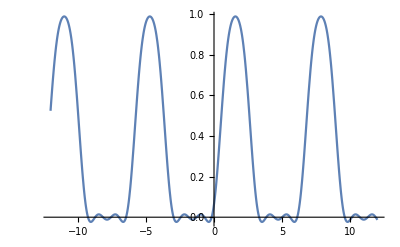

```mathematica
ClearAll["Global`*"]

sinHalfWave=Piecewise[{{Sin[ωt],Sin[ωt]>0},{0,Sin[ωt]<0}}];
series4th=FourierSeries[sinHalfWave,ωt,4];

Print["The following graph represents the Fourier Series expansion of the Sine Half-Wave to the 4th order:"]
Plot[series4th,{ωt,-12,12}]
```

```mathematica
Remove["Global`*"]

ω=1;
Radius=1;
t=ϕ;

xDiffEq=x''[t]==ω^2 *x[t]+2*ω* y'[t];
yDiffEq=y''[t]==ω^2 *y[t]-2*ω *x'[t];

DSolve[{xDiffEq,yDiffEq,x[0]==-(1/2),x'[0]==Vo*Cos[θ],y[0]==0,y'[0]==Vo*Sin[θ]},{x[t],y[t]},t]//FullSimplify;

xEquation=Vo ϕ Cos[θ-ϕ]-Cos[ϕ]/2-1/2 ϕ Sin[ϕ];
yEquation=1/2 (-ϕ Cos[ϕ]+2 Vo ϕ Sin[θ-ϕ]+Sin[ϕ]);
```

```mathematica
Vo=1.5;
θ=Pi/2;

Show[ParametricPlot[{Cos[z],Sin[z]},{z,0,2π}],ParametricPlot[{xEquation,yEquation},{ϕ,0,0.86}]]
```

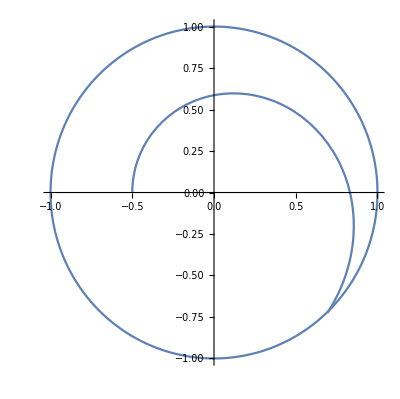

```mathematica
Clear[Vo,θ];
Vo=0.8;
θ=Pi/2;
Show[ParametricPlot[{Cos[z],Sin[z]},{z,0,2π}],ParametricPlot[{xEquation,yEquation},{ϕ,0,2.9}]]
```

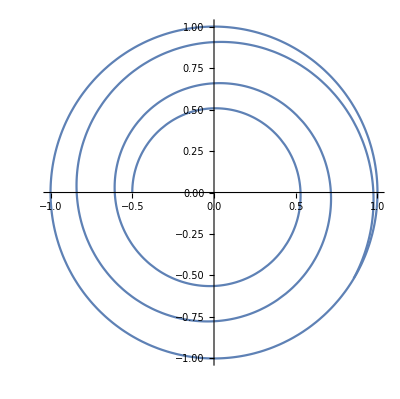

```mathematica
Clear[Vo,θ]
Vo=0.45;
θ=Pi/2;

Show[ParametricPlot[{Cos[z],Sin[z]},{z,0,2π}],ParametricPlot[{xEquation,yEquation},{ϕ,0,17.3}]]
```

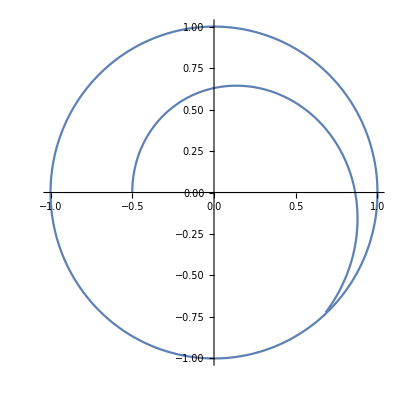

```mathematica
Clear[Vo,θ]
Vo=0.328;
θ=Pi/2;
Show[ParametricPlot[{Cos[z],Sin[z]},{z,0,2π}],ParametricPlot[{xEquation,yEquation},{ϕ,0,5}]]
```

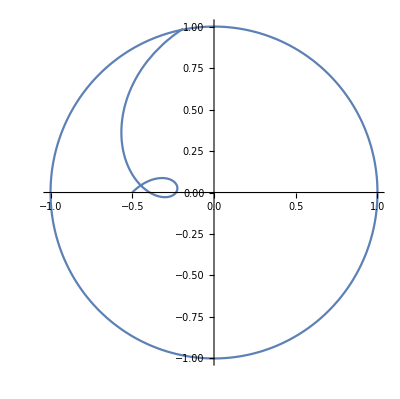

```mathematica
Clear[Vo,θ]
Vo=0.47;
θ=Pi/4;
Show[ParametricPlot[{Cos[z],Sin[z]},{z,0,2π}],ParametricPlot[{xEquation,yEquation},{ϕ,0,3.83}]]
```

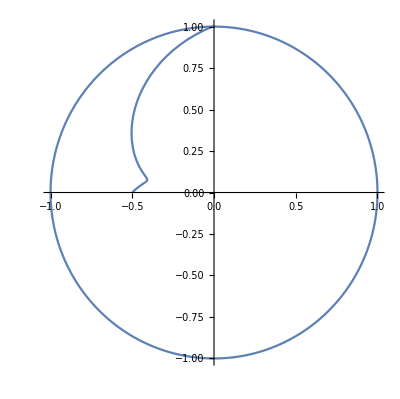

```mathematica
Clear[Vo,θ]
Vo=0.283;
θ=Pi/4;
Show[ParametricPlot[{Cos[z],Sin[z]},{z,0,2π}],ParametricPlot[{xEquation,yEquation},{ϕ,0,3.3}]]
```

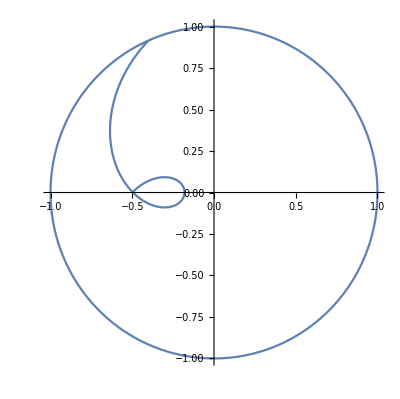

```mathematica
Clear[Vo,θ]
Vo=0.51;
θ=Pi/4;
Show[ParametricPlot[{Cos[z],Sin[z]},{z,0,2π}],ParametricPlot[{xEquation,yEquation},{ϕ,0,3.75}]]

(* Did not solve any equations, just played around with the plot values. *)
(* The initial velocity for this effect appears to be about 0.51 m/s. *)
(* The puck exits the merry-go-round at about 3.75 seconds. *)
```